```mathematica
Quit[];
```

## License

```mathematica
(* 
    Mathematica script to calculate the energy of skyrmions as well as their stable radius, DW width, etc.
    Copyright (C) 2018  Felix Buettner (felixbuettner@gmail.com)

    This program is free software: you can redistribute it and/or modify
    it under the terms of the GNU General Public License as published by
    the Free Software Foundation, either version 3 of the License, or
    (at your option) any later version.

    This program is distributed in the hope that it will be useful,
    but WITHOUT ANY WARRANTY; without even the implied warranty of
    MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.  See the
    GNU General Public License for more details.

    You should have received a copy of the GNU General Public License
    along with this program.  If not, see <http://www.gnu.org/licenses/>. 
*)
```

## Load module

```mathematica
SetDirectory[NotebookDirectory[]];
<<CombinedEnergiesInterfacialDMI`
```

## General comment on units

We use a variant of SI units where the base unit is nm instead of m. This is done because the numerical code is much more robust if all energy coefficients have the same order of magnitude. To convert, just replace all instances of “m” by "10^9nm". In particular:
A = 1e-11 A/m = 1e-11 A/(1e9 nm) = 1e-20 A/nm (multiply SI unit by 10^-9)
Ku = 1e6 J/m^3 = 1e6 J/(1e27 nm^3) = 1e-21 J/nm^3 (multiply SI unit by 10^-27)
Di = 1e-3 J/m^2 = 1e-3 J/(1e18 nm^2) = 1e-21 J/nm^2 (multiply SI unit by 10^-18)
Ms = 1e6 A/m = 1e6 A/(1e9 nm) = 1e-3 A/nm (multiply SI unit by 10^-9)
μ0 = 4π 10^-7 Vs/Am = 4π 10^-7 Vs/(10^9A-nm) = 4π 10^-16 Vs/(A-nm) (multiply SI unit by 10^-9)
Bz = μ0 Hz = 1T = 1 J/Am^2 = 10^-18 J/(A-nm^2) (multiply SI unit by 10^-18)
Of course, one can easily define SI wrapper functions:

```mathematica
CollapseRadiusMinimumEnergyBarrierSI[t_,p_,nl_,A_,Ku_,Di_,Ms_,Ebmin_,temperature_,Bzmin_,kTfactor_]:=CollapseRadiusMinimumEnergyBarrierVerbose3[t 10^9,p 10^9,nl,A 10^-9,Ku 10^-27,Di 10^-18,Ms 10^-9,Ebmin,temperature,Bzmin 10^-18,kTfactor]
```

## Example 1 : Calculate R (Bz)

See section "General comment on units" for the reason of the 10^-9 factors after the magnetic units

"result" contains three lists: "extrema", "minima", and "stableMinima".
Typically, "stableMinima" are most interesting. 
"stableMinima" is a list, where each element is a list of all stable minima
corresponding to a certain applied field value. Each minimum is defined 
by a list of replacement rules. 

Example:
minimum={"count"→1,"type"→1,"block"→1,"Bz"→-2.17817×10^-20,"R"→2661.71,"Δ"→3.13325,"ψ"→0.0000141421,"energy"→-83297.2,"Eb"→83324.6,"Ebreverse"→∞,"Ebannihilation"→83324.6,"howStabilized"→"strayfield"}

Explanations of the elements of “minimum”

Bz is in Vs/(A-nm). To convert it to Tesla, multiply by 10^18.
R and Δ are in nm, ψ is in rad.
Energies are in multiples of Ad, where d is the total thickness of magnetic material (d=t*nl).
Eb is the energy barrier to the next smaller radius minimum, or to R=0, if no such minimum exists.
Ebreverse is the energy barrier to the next larger radius minimum, or to R=∞, if no such minimum exists.
Ebannihilation is the minimum of Eb and Ebreverse. This value is compared to kT*temperature*kTfactor to determine if the minimum is stable.
If two minima have the same “block” number, then they are mutually accessible by thermal energy (i.e., they form a zero stiffness skyrmion).
howStabilized should say if the minimum is stabilized by DMI or stray fields. However, this code is still not correctly implemented.

```mathematica
result=Block[{
t=1(* single magnetic layer thickness *),
p=4 (* layer peridicity (one magnetic layer + one non-magnetic spacer *),
nl=40 (* number of repeats *),
A=10 10^-12 10^-9 (* exchange constant, in J/nm *),
Ku=1.724 10^6 10^-27 (* anisotropy constant (crystal anisotropy, not Keff), in J/nm^3 *),
Di=2 10^-3 10^-18 (* interfacial DMI constant, in J/nm^2 *),
Ms=1.4 10^6 10^-9 (* saturation magnetization, in A/nm *),
μ0=4π 10^-7 10^-9 (* vacuum permeability, in Vs/(A-nm) *),
Ebmin=2 (* energy barriers, in multiples of Ad, that can be "tunneled through" via deformations that are not captured by the model *),
temperature=300 (* temperature in K *),
Bzmin=-0 10^-18, (* field at which the R(Bz) curve is started. Note that Bz is negative and in J/(A-nm^2). A value of 0 means "determine suitable starting condition automatically". *),
kTfactor=50 (* Skyrmions with energy barriers < kTfactor*temperature are considered unstable. *)
},
Print["Quality factor Q = "<>ToString[2Ku/(μ0*Ms^2)]];
CollapseRadiusMinimumEnergyBarrierVerbose3[t,p,nl,A,Ku,Di,Ms,Ebmin,temperature,Bzmin,0]];
```

Quality factor Q = 1.39991

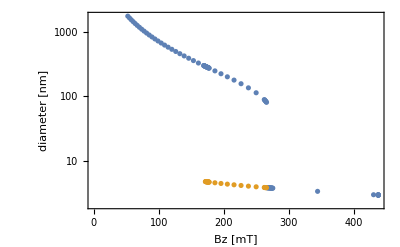

```mathematica
(* Plot the largest (blue) and smallest (orange) minimum diameter as a function of Bz. Between 160 mT and 250 mT, two minima co-exist and there is some hysteresis when cycling the field. *)
Block[{Bzmin=50,Bzmax=3000 (* field range, in absolute values and in mT *)},
ListLogPlot[{
Select[First@Flatten[{-10^21"Bz",2"R"}/.#&/@("stableMinima"/.result),{2}],#[[1]]<Bzmax&&#[[1]]>Bzmin&],
Select[Last@Flatten[{-10^21"Bz",2"R"}/.#&/@("stableMinima"/.result),{2}],#[[1]]<Bzmax&&#[[1]]>Bzmin&]
},
Frame->True,
FrameLabel->{"Bz [mT]","diameter [nm]"}]]
```

## Plot E (R)

```mathematica
(* For the bistability region in the previous example, we plot E(R). The warning can be ignored. *)
```

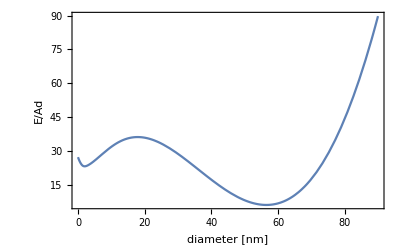

```mathematica
Block[{
t=1(* single magnetic layer thickness *),
p=4 (* layer peridicity (one magnetic layer + one non-magnetic spacer *),
nl=40 (* number of repeats *),
A=10 10^-12 10^-9 (* exchange constant, in J/nm *),
Ku=1.724 10^6 10^-27 (* anisotropy constant (crystal anisotropy, not Keff), in J/nm^3 *),
Di=2 10^-3 10^-18 (* interfacial DMI constant, in J/nm^2 *),
Ms=1.4 10^6 10^-9 (* saturation magnetization, in A/nm *),
μ0=4π 10^-7 10^-9 (* vacuum permeability, in Vs/(A-nm) *),
Bz=-0.25 10^-18 (* Bz in Vs/(A-nm). Remember: Bz is negative. *)
},
Plot[EofR[R,t,p,nl,A,Ku,Di,Ms,Bz],{R,0,90},PlotRange->All,
Frame->True,
FrameLabel->{"diameter [nm]","E/Ad"}]]
```

## Find minima in E (R)

```mathematica
(* Now we want to know the position of minima and maxima in the previous plot. *)
```

```mathematica
extrema=Block[{
t=1(* single magnetic layer thickness *),
p=4 (* layer peridicity (one magnetic layer + one non-magnetic spacer *),
nl=40 (* number of repeats *),
A=10 10^-12 10^-9 (* exchange constant, in J/nm *),
Ku=1.724 10^6 10^-27 (* anisotropy constant (crystal anisotropy, not Keff), in J/nm^3 *),
Di=2 10^-3 10^-18 (* interfacial DMI constant, in J/nm^2 *),
Ms=1.4 10^6 10^-9 (* saturation magnetization, in A/nm *),
μ0=4π 10^-7 10^-9 (* vacuum permeability, in Vs/(A-nm) *),
Bz=-0.25 10^-18 (* Bz in Vs/(A-nm). Remember: Bz is negative. *)
},
FindAllExtrema[t,p,nl,A,Ku,Di,Ms,Bz]]
```

{mins→{{Bz→-2.5×10^-19,R→2.00095,Δ→2.11253,ψ→0.0000141421,energy→23.2828},{Bz→-2.5×10^-19,R→56.4966,Δ→3.09669,ψ→0.0000141421,energy→6.18377}},maxs→{{Bz→-2.5×10^-19,R→17.9036,Δ→3.04673,ψ→0.0000141421,energy→36.2251}}}

```mathematica
(* We can also select the minima and determine their energy barriers automatically. *)
DetermineEnergyBarriers[extrema]
```

{{Bz→-2.5×10^-19,R→2.00095,Δ→2.11253,ψ→0.0000141421,energy→23.2828,Eb→4.0428,Ebreverse→12.9424,Ebannihilation→4.0428},{Bz→-2.5×10^-19,R→56.4966,Δ→3.09669,ψ→0.0000141421,energy→6.18377,Eb→30.0414,Ebreverse→∞,Ebannihilation→30.0414}}